```mathematica
(*Generate a Discrete data composed of first 10 +ve odd integers and their Cubes.Graph this data(discrete data mean in the form of list).*)
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

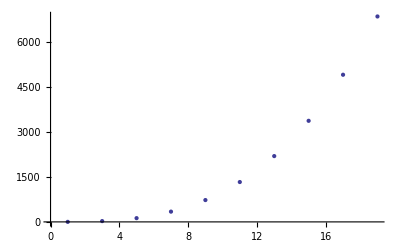

```mathematica
a=Table[{2i-1,(2i-1)^3},{i,1,10}];
ListPlot[a]
```

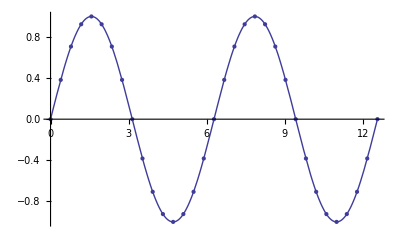

```mathematica
(* Graph Sinx for 0=<x<=4Pi and its discretized(Graph to the points)version with a step size of Pi/8 rad.and Display both Graphs together.*)
g1=Plot[Sin[x],{x,0,4Pi}];
g2=ListPlot[Table[{x,Sin[x]},{x,0,4Pi,Pi/8}]];
Show[g1,g2]
```

```mathematica
(* 2D Commands*)
```

```mathematica
?Circle
```

Circle[{x,y},r] is a two-dimensional graphics primitive that represents a circle of radius r centered at the point x, y. 
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},r,{θ_1,θ_2}] gives a circular arc. 
Circle[{x,y},{r_x,r_y}] gives an ellipse with semi-axes of lengths r_x and r_y, oriented parallel to the coordinate axes.

```mathematica
?Disk
```

RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] is a two-dimensional graphics primitive that represents a filled disk of radius StyleBox["r", "TI"] centered at the point StyleBox["x", "TI"], StyleBox["y", "TI"]. 
RowBox[{"Disk", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a disk of radius 1. 
RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox["θ", StyleBox["1", "TR"]], ",", SubscriptBox["θ", StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a segment of a disk. 
RowBox[{"Disk", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an elliptical disk with semi-axes of lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]], oriented parallel to the coordinate axes.

```mathematica
?Rectangle
```

Rectangle[{x_min,y_min},{x_max,y_max}] is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes. 
Rectangle[{x_min,y_min}] corresponds to a unit square.